```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/ece1228-electromagnetic-theory"]
fs=Style[#,FontSize->14]&;
```

/Users/pjoot/project/figures/ece1228-electromagnetic-theory

ps5. p1.

```mathematica
ClearAll[ AlGaN, chi ]

AlGaN = {
"omega_0"->1.921 10^14,
"omega_p"->3.328 10^14,
"gamma" -> 9.756 10^12
} ;

(* χ(ω) =Subscript[ω, p]^2/(Subscript[ω, 0]^2-ω^2+ j γ ω) *)
chi[omega_, medium_] := Module[{omegap, omega0, gamma}, {omegap, omega0, gamma} ={"omega_p", "omega_0", "gamma"} /. medium ;omegap^2/(omega0^2 - omega^2 + I gamma omega) 
]
```

a) Index of refraction

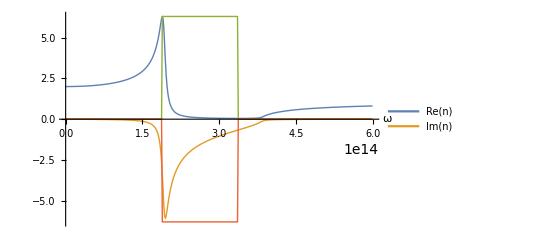

{p1IndexOfRefractionFig1.eps,p1IndexOfRefractionFig1pn.png}

```mathematica
ClearAll[ p1a, nAlGaNpoints, epsilonrAlGaN, nAlGaNpointsRe, nAlGaNpointsIm, epsilonrAlGaNpoints, txPoints, maxN, sgn, absMaxOfSecondInListsOfPairs]
epsilonrAlGaN[omega_] := 1 +chi[omega, AlGaN] ;

epsilonrAlGaNpoints = Table[ {o, epsilonrAlGaN[o]}, {o, 0, 6 10^14, 6 10^14/400}] ;
txPoints[p_, f_] := {p[[#]] // First, (p[[#]] //Last)// f} &/@ Range[Length[p]]  ;
nAlGaNpoints = txPoints[epsilonrAlGaNpoints, Sqrt] ;
nAlGaNpointsRe= txPoints[nAlGaNpoints, Re] ;
nAlGaNpointsIm = txPoints[nAlGaNpoints, Im] ;

absMaxOfSecondInListsOfPairs[p1_, p2_] := {p1// Transpose // Last // Abs // Max, p2// Transpose // Last // Abs  // Max} // Max ;
maxN = absMaxOfSecondInListsOfPairs[nAlGaNpointsRe,nAlGaNpointsIm];
sgn[e_, s_] := {e[[#]] // First, s Boole[Sign[(e[[#+1]]//Last) - (e[[#]] // Last)] ==-1]} &/@ Range[Length[e]-1] ;

p1a =ListLinePlot[{nAlGaNpointsRe, nAlGaNpointsIm, sgn[nAlGaNpointsRe, maxN], sgn[nAlGaNpointsRe,-maxN]},PlotLegends-> Placed[LineLegend[{"Re(n)"//fs, "Im(n)"//fs}],{Right,Top}],
PlotRange -> Full,
PlotStyle-> Thick,
AxesLabel-> {"ω" //fs, ""}] 

peeters`exportForLatex["p1IndexOfRefractionFig1", p1a]
```

b) relative permittivity

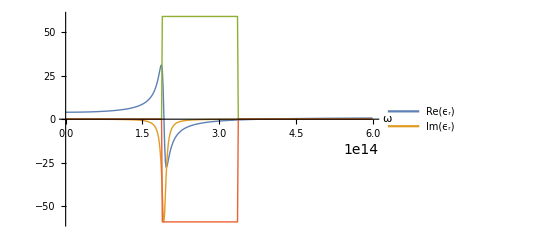

{p1EpsilonRFig2.eps,p1EpsilonRFig2pn.png}

```mathematica
ClearAll[epsilonrAlGaNpointsRe, epsilonrAlGaNpointsIm, maxE,p1b]

epsilonrAlGaNpointsRe= txPoints[epsilonrAlGaNpoints, Re] ;
epsilonrAlGaNpointsIm = txPoints[epsilonrAlGaNpoints, Im] ;
maxE = absMaxOfSecondInListsOfPairs[epsilonrAlGaNpointsRe,epsilonrAlGaNpointsIm];

p1b = ListLinePlot[{epsilonrAlGaNpointsRe,epsilonrAlGaNpointsIm,sgn[nAlGaNpointsRe, maxE], sgn[nAlGaNpointsRe,-maxE]},PlotLegends-> Placed[LineLegend[{"Re(ϵ_r)"//fs, "Im(ϵ_r)"//fs}],{Right,Top}],
PlotRange -> Full,
PlotStyle-> Thick,
AxesLabel-> {"ω"//fs, ""}]

peeters`exportForLatex["p1EpsilonRFig2", p1b]
```

ps5. p2.

```mathematica
ClearAll[ ammonia1,ammonia2 ,omegac ,sevenGhz ,permittivityAm,nAm]

ammonia1 = {
"omega_0"->2.4165825 10^15,
"omega_p"->10 10^9,
"gamma" -> 5 10^9
} ;

ammonia2 = {
"omega_0"->2.4166175 10^15,
"omega_p"->10 10^9,
"gamma" -> 5 10^9
} ;

omegac = 2.4166 10^15 ;
sevenGhz = 7 10^9 ;

(*toggled sign for active medium Subscript[ω, p,k]-> j Subscript[ω, p,k], or  Subscript[ω, p,k]^2->  -Subscript[ω, p,k]^2*)
permittivityAm[omega_] := 1 - chi[omega, ammonia1] - chi[omega, ammonia2] ;
nAm[nuDetuning_] := Sqrt[ permittivityAm[2 Pi nuDetuning + omegac]] ;
```

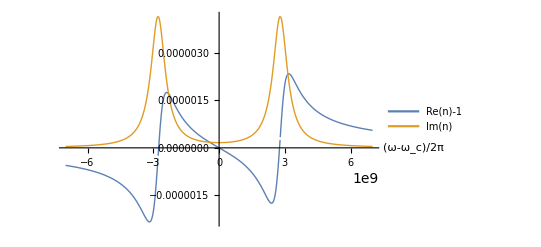

{p2nFig3.eps,p2nFig3pn.png}

```mathematica
ClearAll[p2n]

p2n = Plot[{(nAm[nu]// Re) -1, (nAm[nu]// Im) -0},{nu, -sevenGhz, sevenGhz}, PlotLegends-> Placed[LineLegend[{"Re(n)-1"//fs, "Im(n)"//fs}],{Right,Top}],
PlotRange -> Full,
PlotStyle->Thick,
AxesLabel-> {"(ω-ω_c)/2π"//fs, ""}
]

peeters`exportForLatex["p2nFig3", p2n]
```